```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
temp80 = Delete[Import["E:\Google Drive\Advanced_Lab\Diode\meas/temp80","table"],{1}] ;
temp90 = Delete[Import["E:\Google Drive\Advanced_Lab\Diode\meas/temp90","table"],{1}] ;
temp100 = Delete[Import["E:\Google Drive\Advanced_Lab\Diode\meas/temp100","table"],{1}] ;
temp110 = Delete[Import["E:\Google Drive\Advanced_Lab\Diode\meas/temp110","table"],{1}] ;
temp120 = Delete[Import["E:\Google Drive\Advanced_Lab\Diode\meas/temp120","table"],{1}] ;
temp130 = Delete[Import["E:\Google Drive\Advanced_Lab\Diode\meas/temp130","table"],{1}] ;
temp140 = Delete[Import["E:\Google Drive\Advanced_Lab\Diode\meas/temp140","table"],{1}] ;
temp150 = Delete[Import["E:\Google Drive\Advanced_Lab\Diode\meas/temp150","table"],{1}] ;
temp160 = Delete[Import["E:\Google Drive\Advanced_Lab\Diode\meas/temp160","table"],{1}] ;
temp170 = Delete[Import["E:\Google Drive\Advanced_Lab\Diode\meas/temp170","table"],{1}] ;
temp180 = Delete[Import["E:\Google Drive\Advanced_Lab\Diode\meas/temp180","table"],{1}] ;
temp192 = Delete[Import["E:\Google Drive\Advanced_Lab\Diode\meas/temp192","table"],{1}] ;
temp200 = Delete[Import["E:\Google Drive\Advanced_Lab\Diode\meas/temp200","table"],{1}] ;
temp210= Delete[Import["E:\Google Drive\Advanced_Lab\Diode\meas/temp210","table"],{1}] ;
temp220 = Delete[Import["E:\Google Drive\Advanced_Lab\Diode\meas/temp220","table"],{1}] ;
temp230 = Delete[Import["E:\Google Drive\Advanced_Lab\Diode\meas/temp230","table"],{1}] ;
temp250 = Delete[Import["E:\Google Drive\Advanced_Lab\Diode\meas/temp250","table"],{1}] ;
temp270 = Delete[Import["E:\Google Drive\Advanced_Lab\Diode\meas/temp270","table"],{1}] ;
temp297 = Delete[Import["E:\Google Drive\Advanced_Lab\Diode\meas/temp297","table"],{1}] ;
```

```mathematica
{m1,m2,m3,m4}=Graphics/@{Circle[{0,0},1],Disk[{0,0},1],Line[{{-0.5,-0.5},{0.5,-0.5},{0.5,0.5},{-0.5,0.5},{-0.5,-0.5}}],Polygon[{{-0.5,-0.5},{0.5,-0.5},{0.5,0.5},{-0.5,0.5}}]};
```

```mathematica
dataplot = ListPlot[{temp80,temp90,temp100,temp110,temp120,temp130,temp140,temp150,temp160,temp170,temp180,temp192,temp200,temp210,temp220,temp230,temp250,temp270,temp297}, ImageSize -> Large, Frame -> True, FrameLabel -> {"Voltage","Current"}, GridLines-> Automatic, GridLinesStyle->Directive[Gray,Dashed]];
```

```mathematica
fit80 = NonlinearModelFit[temp80,S(ⅇ^((1.60217657×10^-19 *V)/(1.3806488×10^-23 * (80.565)))), {S},V];
fit90 = NonlinearModelFit[temp90, S(ⅇ^((1.60217657×10^-19 *V)/(1.3806488×10^-23 * (90.16)))), {S},V];
fit100 = NonlinearModelFit[temp100, S(ⅇ^((1.60217657×10^-19 *V)/(1.3806488×10^-23 * (99.375)))), {S},V];
fit110 = NonlinearModelFit[temp110, S(ⅇ^((1.60217657×10^-19 *V)/(1.3806488×10^-23 * (111.055)))), {S},V];
fit120 = NonlinearModelFit[temp120, S(ⅇ^((1.60217657×10^-19 *V)/(1.3806488×10^-23 * (119.93)))), {S},V];
fit130 = NonlinearModelFit[temp130, S(ⅇ^((1.60217657×10^-19 *V)/(1.3806488×10^-23 * (131.17)))), {S},V];
fit140 = NonlinearModelFit[temp140, S(ⅇ^((1.60217657×10^-19 *V)/(1.3806488×10^-23 * (140.155)))), {S},V];
fit150 = NonlinearModelFit[temp150, S(ⅇ^((1.60217657×10^-19 *V)/(1.3806488×10^-23 * (150.7)))), {S},V];
fit160 = NonlinearModelFit[temp160, S(ⅇ^((1.60217657×10^-19 *V)/(1.3806488×10^-23 * (160.4)))), {S},V];
fit170 = NonlinearModelFit[temp170, S(ⅇ^((1.60217657×10^-19 *V)/(1.3806488×10^-23 * (171.095)))), {S},V];
fit180 = NonlinearModelFit[temp180, S(ⅇ^((1.60217657×10^-19 *V)/(1.3806488×10^-23 * (178.71)))), {S},V];
fit192 = NonlinearModelFit[temp192, S(ⅇ^((1.60217657×10^-19 *V)/(1.3806488×10^-23 * (191.735)))), {S},V];
fit200 = NonlinearModelFit[temp200, S(ⅇ^((1.60217657×10^-19 *V)/(1.3806488×10^-23 * (200.65)))), {S},V];
fit210 = NonlinearModelFit[temp210, S(ⅇ^((1.60217657×10^-19 *V)/(1.3806488×10^-23 * (211.055)))), {S},V];
fit220 = NonlinearModelFit[temp220, S(ⅇ^((1.60217657×10^-19 *V)/(1.3806488×10^-23 * (220.04)))), {S},V];
fit230 = NonlinearModelFit[temp230, S(ⅇ^((1.60217657×10^-19 *V)/(1.3806488×10^-23 * (233.97)))), {S},V];
fit250 = NonlinearModelFit[temp250, S(ⅇ^((1.60217657×10^-19 *V)/(1.3806488×10^-23 * (251.29)))), {S},V];
fit270 = NonlinearModelFit[temp270, S(ⅇ^((1.60217657×10^-19 *V)/(1.3806488×10^-23 * (270.25)))), {S},V];
fit297 = NonlinearModelFit[temp297, S(ⅇ^((1.60217657×10^-19 *V)/(1.3806488×10^-23 * (297.55)))), {S},V];
```

```mathematica
fitplots = Plot[{Normal[fit80],Normal[fit90],Normal[fit100],Normal[fit110],Normal[fit120],Normal[fit130],Normal[fit140],Normal[fit150],Normal[fit160],Normal[fit170],Normal[fit180],Normal[fit192],Normal[fit200],Normal[fit210],Normal[fit220],Normal[fit230],Normal[fit250],Normal[fit270],Normal[fit297]},{V,0,1.1}, ImageSize -> Large, Frame -> True, FrameLabel -> {"Voltage (V)","Current (A)"}, GridLines-> Automatic, GridLinesStyle->Directive[Gray,Dashed],PlotRange -> {0, 0.002}];
```

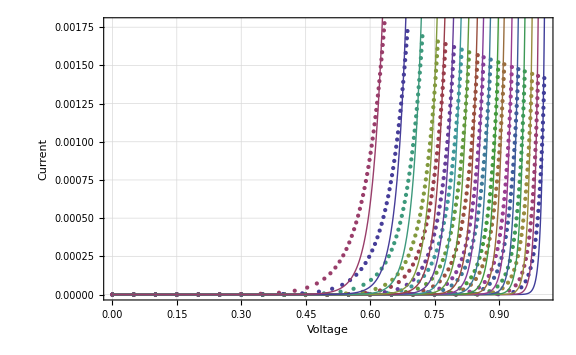

```mathematica
Show[dataplot,fitplots]
```

```mathematica
fit80
```

FittedModel[2.19142×10^-66 ⅇ^(«19» V)]

```mathematica
fit80["ParameterTableEntries"]
```

{{2.19142×10^-66,8.71046×10^-68,25.1585,1.12978×10^-29}}

```mathematica
fit80["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
S | 2.19142×10^-66 | 8.71046×10^-68 | 25.1585 | 1.12978×10^-29

```mathematica
data ={Delete[fit80["ParameterTableEntries"][[1]],{{3},{4}}],Delete[fit90["ParameterTableEntries"][[1]],{{3},{4}}],Delete[fit100["ParameterTableEntries"][[1]],{{3},{4}}],Delete[fit110["ParameterTableEntries"][[1]],{{3},{4}}],Delete[fit120["ParameterTableEntries"][[1]],{{3},{4}}],Delete[fit130["ParameterTableEntries"][[1]],{{3},{4}}],Delete[fit140["ParameterTableEntries"][[1]],{{3},{4}}],Delete[fit150["ParameterTableEntries"][[1]],{{3},{4}}],Delete[fit160["ParameterTableEntries"][[1]],{{3},{4}}],Delete[fit170["ParameterTableEntries"][[1]],{{3},{4}}],Delete[fit180["ParameterTableEntries"][[1]],{{3},{4}}],Delete[fit192["ParameterTableEntries"][[1]],{{3},{4}}],Delete[fit200["ParameterTableEntries"][[1]],{{3},{4}}],Delete[fit210["ParameterTableEntries"][[1]],{{3},{4}}],Delete[fit220["ParameterTableEntries"][[1]],{{3},{4}}],Delete[fit230["ParameterTableEntries"][[1]],{{3},{4}}],Delete[fit250["ParameterTableEntries"][[1]],{{3},{4}}],Delete[fit270["ParameterTableEntries"][[1]],{{3},{4}}],Delete[fit297["ParameterTableEntries"][[1]],{{3},{4}}]}
```

{{2.19142×10^-66,8.71046×10^-68},{7.03892×10^-59,2.46279×10^-60},{5.01669×10^-53,2.17295×10^-54},{4.70476×10^-47,1.52001×10^-48},{3.51289×10^-43,1.3731×10^-44},{3.26412×10^-39,1.02199×10^-40},{2.87378×10^-36,1.06806×10^-37},{1.60707×10^-33,4.88044×10^-35},{4.01224×10^-31,1.47919×10^-32},{6.37269×10^-29,1.90388×10^-30},{1.98582×10^-27,7.10184×10^-29},{2.81825×10^-25,9.55138×10^-27},{7.33211×10^-24,2.64115×10^-25},{1.95506×10^-22,5.93848×10^-24},{3.37952×10^-21,1.09592×10^-22},{9.37049×10^-20,2.83395×10^-21},{6.81613×10^-18,2.23113×10^-19},{3.28207×10^-16,1.17786×10^-17},{4.0541×10^-14,1.44326×10^-15}}

```mathematica
data[[All,2]]/data[[All,1]]
```

{0.0397479,0.0349882,0.0433145,0.0323078,0.0390875,0.0313099,0.0371658,0.0303685,0.036867,0.0298755,0.0357628,0.0338912,0.0360217,0.0303749,0.0324284,0.0302433,0.0327331,0.0358877,0.0355999}

```mathematica
data
```

{{-151.186,-154.411},{-133.901,-137.254},{-120.424,-123.564},{-106.673,-110.105},{-97.7547,-100.997},{-88.6178,-92.0816},{-81.8374,-85.1298},{-75.5109,-79.0052},{-69.9908,-73.2912},{-64.9229,-68.4337},{-61.4838,-64.8146},{-56.5285,-59.9131},{-53.2698,-56.5934},{-49.9865,-53.4806},{-47.1366,-50.5653},{-43.8141,-47.3126},{-39.5272,-42.9466},{-35.6529,-38.9802},{-30.8365,-34.1719}}

```mathematica
data=Insert[data,0.1041033141,{1,1}];data=Insert[data,80.565,{1,1}];
data=Insert[data,0.5878775383,{2,1}];data=Insert[data,90.16,{2,1}];
data=Insert[data,1.561549711,{3,1}];data=Insert[data,99.375,{3,1}];
data=Insert[data,0.3123099422,{4,1}];data=Insert[data,111.055,{4,1}];
data=Insert[data,1.1267652817,{5,1}];data=Insert[data,119.93,{5,1}];
data=Insert[data,0.6246198844,{6,1}];data=Insert[data,131.17,{6,1}];
data=Insert[data,1.047156865,{7,1}];data=Insert[data,140.155,{7,1}];
data=Insert[data,0.8205790638,{8,1}];data=Insert[data,150.7,{8,1}];
data=Insert[data,1.3472193585,{9,1}];data=Insert[data,160.4,{9,1}];
data=Insert[data,0.9736721728,{10,1}];data=Insert[data,171.095,{10,1}];
data=Insert[data,1.5309310892,{11,1}];data=Insert[data,178.71,{11,1}];
data=Insert[data,0.6429910575,{12,1}];data=Insert[data,191.735,{12,1}];
data=Insert[data,1.457446397,{13,1}];data=Insert[data,200.65,{13,1}];
data=Insert[data,1.0349094163,{14,1}];data=Insert[data,211.055,{14,1}];
data=Insert[data,0.4776504998,{15,1}];data=Insert[data,220.04,{15,1}];
data=Insert[data,4.3478442934,{16,1}];data=Insert[data,233.97,{16,1}];
data=Insert[data,0.7960841664,{17,1}];data=Insert[data,251.29,{17,1}];
data=Insert[data,0.5511351921,{18,1}];data=Insert[data,270.25,{18,1}];
data=Insert[data,0.005,{19,1}];data=Insert[data,297.55,{19,1}];
```

```mathematica
data
```

{{80.565,0.104103,-151.186,-154.411},{90.16,0.587878,-133.901,-137.254},{99.375,1.56155,-120.424,-123.564},{111.055,0.31231,-106.673,-110.105},{119.93,1.12677,-97.7547,-100.997},{131.17,0.62462,-88.6178,-92.0816},{140.155,1.04716,-81.8374,-85.1298},{150.7,0.820579,-75.5109,-79.0052},{160.4,1.34722,-69.9908,-73.2912},{171.095,0.973672,-64.9229,-68.4337},{178.71,1.53093,-61.4838,-64.8146},{191.735,0.642991,-56.5285,-59.9131},{200.65,1.45745,-53.2698,-56.5934},{211.055,1.03491,-49.9865,-53.4806},{220.04,0.47765,-47.1366,-50.5653},{233.97,4.34784,-43.8141,-47.3126},{251.29,0.796084,-39.5272,-42.9466},{270.25,0.551135,-35.6529,-38.9802},{297.55,0.005,-30.8365,-34.1719}}

```mathematica
fit = NonlinearModelFit[data[[All,{1,3}]],b+ -gap/(8.6173324×10^−5* T), {gap,b},T, Weights -> (data[[All,3]]/(Exp[data[[All,4]]]/Exp[data[[All,3]]]))^2 + (data[[All,1]]/data[[All,2]])^2]
```

FittedModel[14.0874-(«19»)/T]

```mathematica
fit["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
gap | 1.15207 | 0.00219239 | 525.487 | 3.08589×10^-37
b | 14.0874 | 0.0923134 | 152.604 | 4.13006×10^-28

```mathematica
final = Delete[Import["E:\Google Drive\Advanced_Lab\Diode\meas/final.csv","csv"],{1}];
```

```mathematica
dataplot2 = ErrorListPlot[ final, ImageSize -> Large, Frame -> True, FrameLabel -> {"Temperature","LN[I_s]"}, GridLines-> Automatic, GridLinesStyle->Directive[Gray,Dashed]];
```

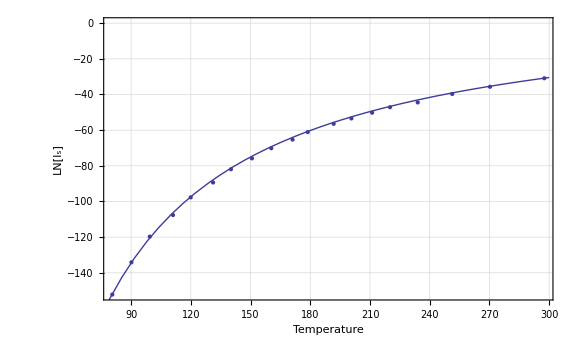

```mathematica
Show[dataplot2, Plot[Normal[fit],{T,0,300}]]
```